```mathematica
(*Exponential Demand: D(p) = Exp(-p*c)*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
Welfare[c1_,c2_,a1_,a2_]:=Module[{R,S,sol,p, W},
(*Revenue change due to new common price p*)
R = (a1*p*Exp[-c1*p] + a2*p*Exp[-c2*p]) - (a1*Exp[-1]/c1 + a2*Exp[-1]/c2);

(*Surplus change due to new common price p*)
S = (a1*Exp[-c1*p]/c1 + a2*Exp[-c2*p]/c2) - (a1*Exp[-1]/c1 + a2*Exp[-1]/c2);

(*Find the optimal new common price p*)
sol = FindRoot[D[R, p]==0,{p, 1/c1}];
p = p/.sol[[1]];

(*Social welfare change due to new common price p*)
W = R + S;
{W,R,S}]
```

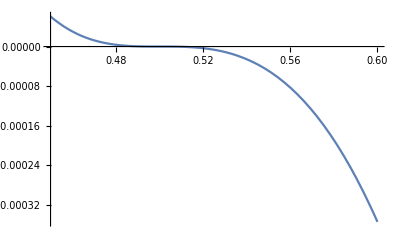

```mathematica
Plot[Welfare[0.5, c2, 2, 1][[1]],{c2,0.45,0.6}]
```